## Structural complexity of functional response models - Part 2

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/general-functional-responses/code/Mathematica/results_a1000m10

```mathematica
Get["FisherMatrix-1_Output_aNInt_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_NInt_k1k2k3"];
```

Get::noopen: Cannot open results/FisherMatrix-1_Output_NInt_k1k2k3.

### Third term - Flexibility - Non-truncated λ

```mathematica
NInts={NIntH1,NIntR,NIntHV,NIntH2,NIntAG,NIntBD,NIntCM,NIntAA}
Labels={"H1","R","HV","H2","AG","BD","CM","AA"};
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
(* Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}]; *)
```

{6.71492,6.22451,11.787,11.1972,10.4422,14.433,14.7811,15.59}

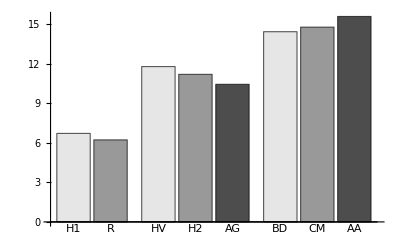
-Graphics-ModelFlexibility

```mathematica
AltLabel2="LN∫_Θ √(det  I (θ))ⅆθ";
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=Labeled[BarChart[lNInts,ChartStyle->{GrayLevel[0.9],GrayLevel[0.6],GrayLevel[0.3]}],
{Style["Model"],Style["Flexibility"]},{Bottom,Left},
RotateLabel->True,
Spacings->{0.4, 1},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["FisherMatrix-2_Output_Complexity_absolute_NonTrunc.pdf",bc1];
```

### Third term - Flexibility - Truncated λ

```mathematica
NInts={NIntH1Trunc,NIntRTrunc,NIntHVTrunc,NIntH2Trunc,NIntAGTrunc,NIntBDTrunc,NIntCMTrunc,NIntAATrunc}
Labels={"H1","R","HV","H2","AG","BD","CM","AA"};
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
(* Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}]; *)
```

{3.8831,3.83281,6.70775,5.76324,5.89872,5.49278,6.10262,8.27634}

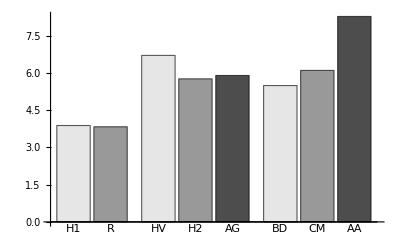
-Graphics-ModelFlexibility

```mathematica
AltLabel2="LN∫_Θ √(det  I (θ))ⅆθ";
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=Labeled[BarChart[lNInts,ChartStyle->{GrayLevel[0.9],GrayLevel[0.6],GrayLevel[0.3]}],
{Style["Model"],Style["Flexibility"]},{Bottom,Left},
RotateLabel->True,
Spacings->{0.4, 1},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["FisherMatrix-2_Output_Complexity_absolute_Trunc.pdf",bc1];
```

### Partial numeric Integration - Truncated λ

```mathematica
PΝprods=Sort[DeleteDuplicates[Join@@Outer[Times,Pvals,Νvals]]]
```

{2,4,8,10,16,20,32,40,64,80,128,160,256,320,512,640,1280}

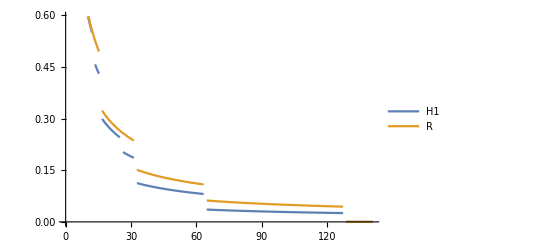

```mathematica
pnk1T=Plot[{
aNIntH1Trunc,
aNIntRTrunc
},
{a,0.01,Max[Max[Νvals]/PΝprods]*1.1},
MaxRecursion->2,
PerformanceGoal->10,
PlotLegends->Placed[{"H1","R"},Above]]
```

```mathematica
pnk2T=Plot[{
aNIntHVTrunc[a],
aNIntH2Trunc[a],
aNIntAGTrunc[a]
},
{a,0.01,200},
MaxRecursion->2,
PerformanceGoal->1,
PlotLegends->Placed[{"HV","H2","AG"},Above]]
```

$Aborted

```mathematica
pnk3T=Plot[{
aNIntBDTrunc[a],
aNIntCMTrunc[a],
aNIntAATrunc[a]
},
{a,0.01,20},
MaxRecursion->2,
PerformanceGoal->1,
PlotLegends->Placed[{"BD","CM","AA"},Above]]
```

$Aborted

```mathematica
pnT=Labeled[GraphicsRow[{pnk1T,pnk2T,pnk3T},ImageSize->Large],{Style["Attack rate"],Style["LN∫_Θ √(det  I (θ))ⅆθ"]},{Bottom,Left},RotateLabel->True,Spacings->{3, 0},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"}]
Export["FisherMatrix-2_Output_partial_numeric_a_Trunc.pdf",pnT];
```

ListLinePlot::nonopt: Options expected (instead of {a,0.01,200}) beyond position 1 in ListLinePlot[{aNIntBDTrunc[a],aNIntCMTrunc[a],aNIntAATrunc[a]},{a,0.01,200},PlotLegends→Placed[{BD,CM,AA},Above]]. An option must be a rule or a list of rules.

-Graphics-Attack rateLN∫_Θ √(det  I (θ))ⅆθ

### Partial numeric Integration - Non-truncated λ

Fix ' a', integrate square root of Expected Fisher Information Matrix over remaining parameters , and take natural log.

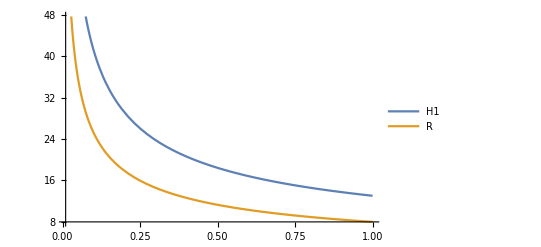

```mathematica
ParmRangeB=Drop[ParmRangeA,1];
precgoal=2;
pnk1=Plot[{
aNIntH1,
aNIntR
},
{a,0.01,1},
PlotLegends->Placed[{"H1","R"},Above]]
```

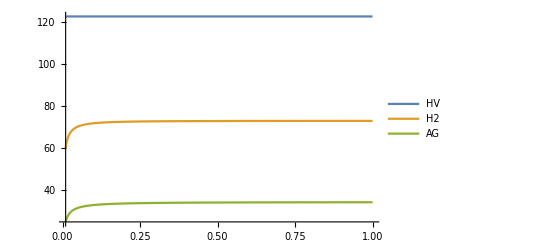

```mathematica
pnk2=Plot[{
aNIntHV,
aNIntH2[a],
aNIntAG[a]
},
{a,0.01,1},
PlotLegends->Placed[{"HV","H2","AG"},Above]]
```

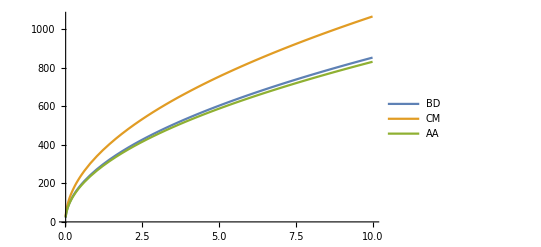

```mathematica
pnk3=Plot[{
aNIntBD[a],
aNIntCM[a],
aNIntAA[a]
},
{a,0.01,10},
PlotLegends->Placed[{"BD","CM","AA"},Above]]
```

```mathematica
pn=Labeled[GraphicsRow[{pnk1,pnk2,pnk3},ImageSize->Large],{Style["Attack rate"],Style["LN∫_Θ √(det  I (θ))ⅆθ"]},{Bottom,Left},RotateLabel->True,Spacings->{3, 0},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"}]
Export["FisherMatrix-2_Output_partial_numeric_a_NonTrunc.pdf",pn];
```

-Graphics-Attack rateLN∫_Θ √(det  I (θ))ⅆθ